#### Kirill Zakharov Linear spline interpolation

x - узлы интерполяции 
f - значения функции в узлах интерполяции

```mathematica
interSplineL[x_,f_]:=Module[{h=Table[x⟦i⟧-x⟦i-1⟧,{i,2,Length@x}]},Table[(x⟦i+1⟧-v)/h⟦i⟧f⟦i⟧+(v-x⟦i⟧)/h⟦i⟧f⟦i+1⟧,{i,1,Length@x-1}]//FullSimplify]
```

pol - построенный сплайн
point - интерполяционная сетка

```mathematica
visualization[pol_,point_]:=Show[{Table[Plot[pol⟦i⟧/.v->k,{k,point⟦i,1⟧,point⟦i+1,1⟧}],{i,1,Length@pol}],Graphics[{PointSize[0.015],Red,Point[point]}]},PlotRange->Full]
```

#### Test 1

```mathematica
x={0,2,3,5,8};
f={1,2,1,4,2};
point={x,f}//Transpose;
```

```mathematica
interSplineL[x,f]
```

{(2+v)/2,4-v,1/2 (-7+3 v),-2/3 (-11+v)}

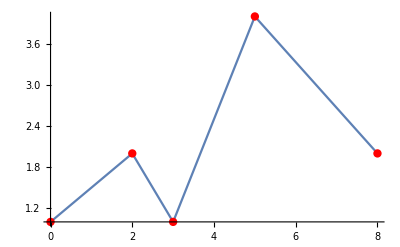

```mathematica
visualization[interSplineL[x,f],point]
```

#### Quadratic spline interpolation

x - узлы интерполяции 
f - значения функции в узлах интерполяции

```mathematica
interSplineQ[x_,f_]:=Module[{coef=Table[Inverse[{{(x⟦i-1⟧)^2,x⟦i-1⟧,1},{(x⟦i⟧)^2,x⟦i⟧,1},{(x⟦i+1⟧)^2,x⟦i+1⟧,1}}].{f⟦i-1⟧,f⟦i⟧,f⟦i+1⟧},{i,2,Length@x-1}]},AppendTo[coef,Inverse[{{(x⟦Length@x-1⟧)^2,x⟦Length@x-1⟧,1},{(x⟦Length@x⟧)^2,x⟦Length@x⟧,1},{0,0,1}}].{f⟦Length@x-1⟧,f⟦Length@x⟧,0}];Table[coef⟦i,1⟧*(v)^2+coef⟦i,2⟧*(v)+coef⟦i,3⟧,{i,1,Length@coef}]]
```

#### Test 1

```mathematica
x2=RandomInteger[{0,10},15]//Sort//DeleteDuplicates;
f2=RandomInteger[{0,10},Length@x2];
point2={x2,f2}//Transpose;
```

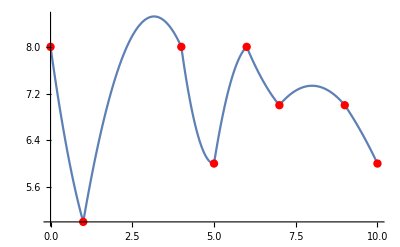

```mathematica
visualization[x2,interSplineQ[x2,f2],point2]
```

#### Test 2

```mathematica
xTest=RandomInteger[{-10,10},100]//DeleteDuplicates//Sort;
fTest=Cos/@xTest;
pointTest={xTest,fTest}//Transpose;
```

```mathematica
polTest=interSplineQ[xTest,fTest]//N
```

{36.1363+7.88599 v+0.418844 v^2,10.7953+1.90269 v+0.066886 v^2,-12.358-4.2991 v-0.346567 v^2,-16.3405-5.53178 v-0.441388 v^2,-7.01084-2.1109 v-0.130399 v^2,1.6067+1.767 v+0.300478 v^2,3.46213+2.84933 v+0.455097 v^2,1.87935+1.53035 v+0.191302 v^2,1.+0.211322 v-0.248376 v^2,1.-0.459698 v^2,1.-0.211322 v-0.248376 v^2,1.87935-1.53035 v+0.191302 v^2,3.46213-2.84933 v+0.455097 v^2,1.6067-1.767 v+0.300478 v^2,-7.01084+2.1109 v-0.130399 v^2,-16.3405+5.53178 v-0.441388 v^2,-12.358+4.2991 v-0.346567 v^2,10.7953-1.90269 v+0.066886 v^2,36.1363-7.88599 v+0.418844 v^2,-0.257203 v+0.0173295 v^2}

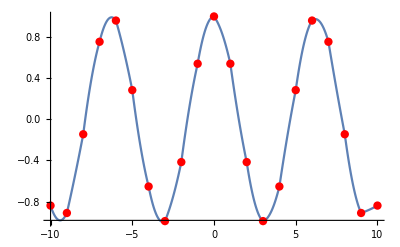

```mathematica
visualization[polTest,pointTest]
```